```mathematica
n := 3
k := (4π *G)/(3*c^2)*ρ0 *(ati)^(3-n)
```

```mathematica
k
```

5.71202×10^-36

```mathematica
a3[t_]:= √(Gcte*Sinh[√(2 k)t]+F Cosh[√(2 k)t])
```

```mathematica
D[a3[t], t]
```

(√2 Gcte √k Cosh[√2 √k t]+√2 F √k Sinh[√2 √k t])/(2 √(F Cosh[√2 √k t]+Gcte Sinh[√2 √k t]))

```mathematica
NSolve[{ati^2 ==Gcte*Sinh[√(2 k)ti]+F Cosh[√(2 k)ti], Dati==√(k/2) (Gcte *Cosh[√(2 k)ti] +F*Sinh[√(2 k)ti])/ati}, {Gcte, F}]
```

{{Gcte→2.47785,F→5.25×10^-20}}

```mathematica
Gcte := 2.477849584928793
F := 5.250000000000016*^-20
```

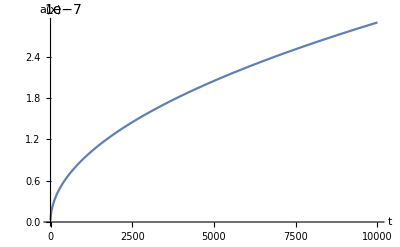

```mathematica
Plot[a3[t], {t, ti, 10000}, AxesLabel->{t,a[x]}]
```

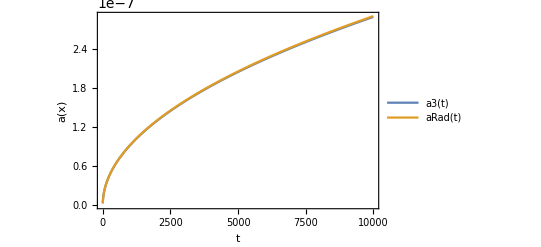

```mathematica
Plot[{a3[t], aRad[t]}, {t, ti, 10000}, PlotLegends->"Expressions", AxesLabel->{t,a[x]}, Frame->True]
```

```mathematica
Export["/home/iara/Documents/doctorado/tres incógnitas/a3aradt.png",%47,"PNG"]
```

/home/iara/Documents/doctorado/tres incógnitas/a3aradt.png

```mathematica
a3sinF[t_]:= √(Gcte*Sinh[√(2 k)t])
```

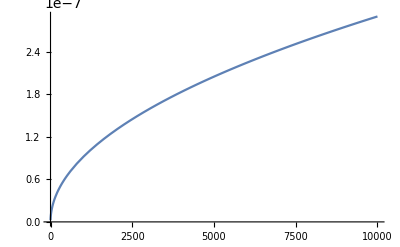

```mathematica
Plot[a3sinF[t], {t, ti, 10000}]
```

```mathematica
√(2/k)
```

5.91725×10^17

```mathematica
Plot[a3[x], {x, 0, ti}]
```

```mathematica
Plot[{a3[t], aRad[t]}, {t, ti, 10000}, PlotLegends->"Expressions", AxesLabel->{t,a[x]}]
```

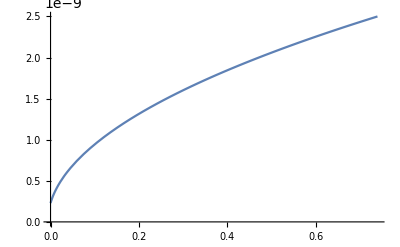
```mathematica
-Graphics-Gcte*Sinh[√(2 k)t]+F Cosh[√(2 k)t] - ar^2*t
```

```mathematica
a3[0]
```

2.29129×10^-10

```mathematica
a3sinF[0]
```

0.

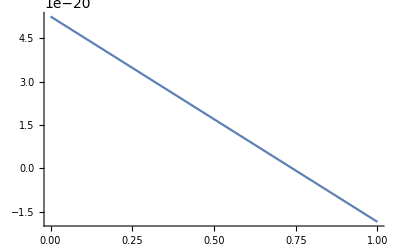

```mathematica
Plot[Gcte*Sinh[√(2 k)t]+F Cosh[√(2 k)t] - ar^2*t, {t, 0, 1}]
```

```mathematica
FindRoot[Gcte*Sinh[√(2 k)t]+F Cosh[√(2 k)t] - ar^2*t==0, {t,1}]
```

{t→0.74}

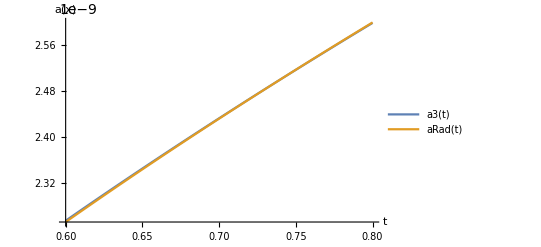

```mathematica
Plot[{a3[t], aRad[t]}, {t, 0.6, 0.8}, PlotLegends->"Expressions", AxesLabel->{t,a[x]}]
```

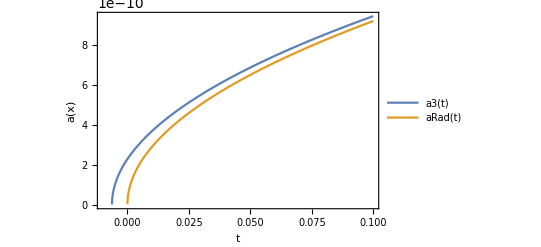

```mathematica
Plot[{a3[t], aRad[t]}, {t, -0.01, 0.1}, PlotLegends->"Expressions", AxesLabel->{t,a[x]}, Frame->True]
```

```mathematica
Export["/home/iara/Documents/doctorado/tres incógnitas/a3aradtchico.png",%81,"PNG"]
```

/home/iara/Documents/doctorado/tres incógnitas/a3aradtchico.png

```mathematica
Export["/home/iara/Documents/doctorado/tres incógnitas/a3aradtchico.png",%50,"PNG"]
```

/home/iara/Documents/doctorado/tres incógnitas/a3aradtchico.png

```mathematica
NSolve[√(Gcte*Sinh[√(2 k)t]+F Cosh[√(2 k)t])==0, t]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.},{t→0.-9.2948×10^17 ⅈ},{t→0.+9.2948×10^17 ⅈ}}

```mathematica
τi = √k*ti
Daτi = 1/(√k)*Dati
```

1.76859×10^-18

7.00842×10^8

```mathematica
a3τ[t_]:= √(X*Sinh[√2 ti]+W Cosh[√2 ti])
```

```mathematica
NSolve[{ati^2 ==X*Sinh[√2 τi]+W Cosh[√2 τi], Daτi==√(1/2) (X *Cosh[√2 τi] +W*Sinh[√2 τi])/ati}, {W, X}]
```

{{W→5.25×10^-20,X→2.47785}}

```mathematica
Clear[W, X]
```

```mathematica
W := 5.250000000000068*^-20
X := 2.477849584928793
```

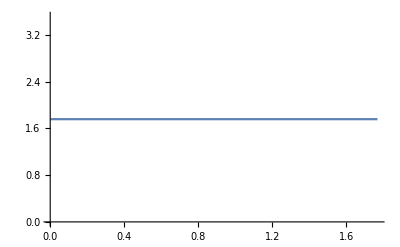

```mathematica
Plot[a3τ[t], {t, τi, 1000*τi}]
```